/home/darya/Method_of_calculation/LabaFifth

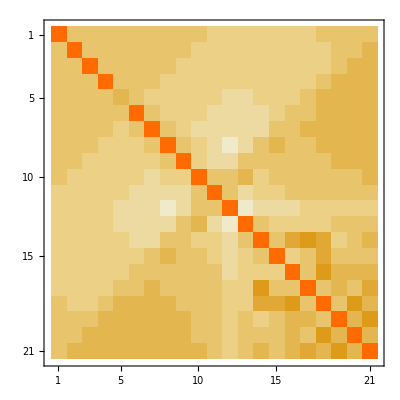

```mathematica
SetDirectory[NotebookDirectory[]]



data= Import["matr.dat"];

Show[MatrixPlot[data] ]
```

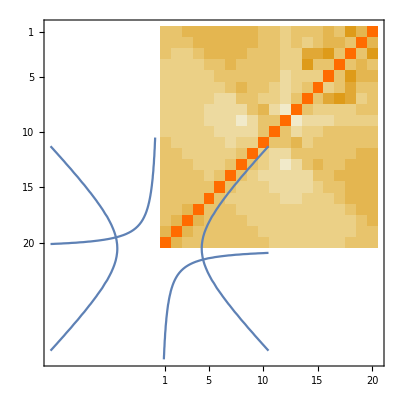

```mathematica
Show[MatrixPlot[data],ContourPlot[x1^2- x2^2-15 == 0,{x1, -10, 10}, {x2,-10,10}], ContourPlot[x1*x2+4 ==0,{x1,-10,10},{x2,-10,10}],Axes->Automatic]
```

```mathematica
dataCoord= Import["coord.dat"];

ticks={{1,"-10"},{2,"-8"},{3,"-6"},{4,"-4"},{5,"-2"},{6,"0"},{7,"2"},{8,"4"},{9,"6"},{10,"8"}, {11,"10"}};
```

```mathematica
ListDensityPlot[data, InterpolationOrder->0,Mesh->None,FrameTicks->{{ticks,None},{ticks,None}}]
```

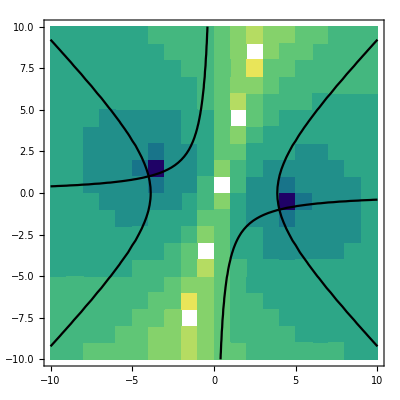

```mathematica
Show[ListDensityPlot[data, InterpolationOrder->0,Mesh->None,DataRange->{{-10,10},{-10,10}},ColorFunction->(ColorData["BlueGreenYellow"])],ContourPlot[x1^2- x2^2-15 == 0,{x1, -10, 10}, {x2,-10,10},ContourStyle->Black], ContourPlot[x1*x2+4 ==0,{x1,-10,10},{x2,-10,10},ContourStyle->Black]]
```

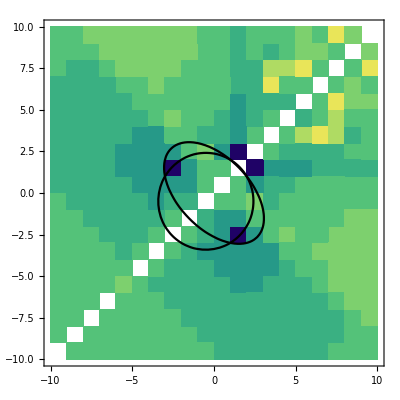

```mathematica
Show[ListDensityPlot[data, InterpolationOrder->0,Mesh->None,DataRange->{{-10,10},{-10,10}},ColorFunction->(ColorData["BlueGreenYellow"])],ContourPlot[x1^2+ x2^2+ x1 + x2 -8 == 0,{x1, -10, 10}, {x2,-10,10},ContourStyle->Black], ContourPlot[x1^2+ x2^2+ x1 * x2 - 7 ==0,{x1,-10,10},{x2,-10,10},ContourStyle->Black]]
```